```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/notatki/programming/mathematica/TRQS

```mathematica
quantis=Import["quantis.dat"];
pseudo=Import["pseudo.dat"];
quantisNoHW=Import["quantisNoHW.dat"];
```

```mathematica
logs=Union[Ceiling[Log10[quantisᵀ[[2]]]],Floor[Log10[quantisNoHWᵀ[[2]]]],{-5}];
yposs=Map[10^#&,logs];
yticks={yposs,logs}ᵀ
```

{{1/100000,-5},{1/10000,-4},{1/1000,-3},{1/100,-2},{1/10,-1},{1,0},{10,1},{100,2},{1000,3},{10000,4},{100000,5}}

```mathematica
fakeData1=Table[10^5,{7}];
fakeData2=Table[10^-5,{7}];
```

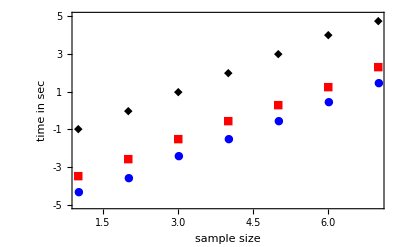

```mathematica
timingsPlot=ListLogPlot[{pseudo,quantisNoHW,quantis,fakeData1,fakeData2},
Frame->True,
FrameTicks->{{yticks,None},{Automatic,None}},
PlotStyle->{Blue,Red,Black,None,None},PlotMarkers->{Automatic,Medium},FrameLabel->{"sample size","time in sec"},LabelStyle->Medium
]
```

```mathematica
Export["/home/jam/Kuweta/notatki/quantum/quantis_random_states/cpc_v2/plots/timingsPlot.pdf",timingsPlot]
```

/home/jam/Kuweta/notatki/quantum/quantis_random_states/cpc_v2/plots/timingsPlot.pdf